## Prep

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/WhyMathematica/misc

```mathematica
imgSize=700;
```

The purpose of this is not only to demonstrate how to do iteration as usual but also to demonstrate the idea that we can traslate itration idea to something else.

## Iteration

可以实现循环的（部分）

Do, For, Table, Map, MapThread, Scan
Fold, FoldList
Nest, NestList
Module

尽量不使用 Do, For 这类循环。另外，Do 比 For 快。例如,

```mathematica
t=x;Do[t=1/(1+t),{5}];t
```

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

Can be translated to

## Example

### Monte Carlo

#### Cal Pi Directly

http://reference.wolfram.com/language/howto/PerformAMonteCarloSimulation.html

Dimension of the random matrix.

```mathematica
mcPi1Dim=100000;
```

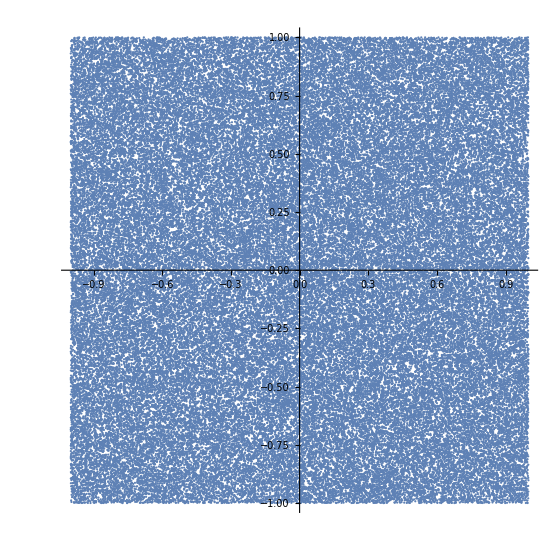

```mathematica
mcPi1Rand=RandomReal[{-1,1},{mcPi1Dim,2}];
ListPlot[mcPi1Rand,AspectRatio->1]
```

```mathematica
mcPi1=4 Count[Map[Norm,mcPi1Rand],_?(#≤1&)]/mcPi1Dim//N
```

3.13824

### An integration of a function

https://en.wikipedia.org/wiki/Monte_Carlo_integration#Wolfram_Mathematica_Example

All functions starts with a name mcInt in this part.

Number of random variables

```mathematica
mcIntRVN=10;
```

The function we want to integrate (integrate from 0.8 to 3 over x)

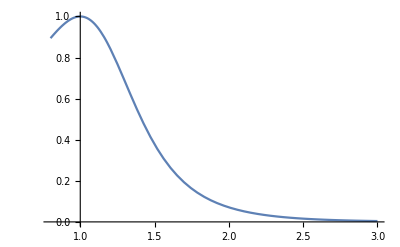

```mathematica
mcIntfunc[x_]:=1/(1+Sinh[2*x]*(Log[x])^2);
mcIntfuncPlt=Plot[mcIntfunc[x],{x,0.8,3}]
```

Find a distribution that we can integrate analytically, like a normal distribution,

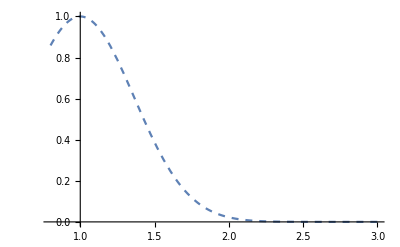

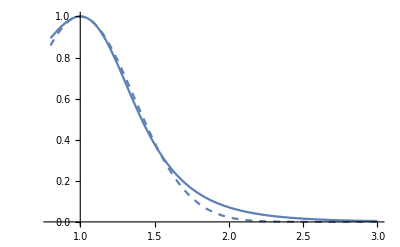

```mathematica
Plot[PDF[NormalDistribution[1,0.399],1.1*x-0.1],{x,0.8,3},PlotStyle->Dashed]
Show[mcIntfuncPlt,%]
```

Generate random list/table

```mathematica
mcIntRV=RandomVariate[PDF[NormalDistribution[1,0.5]],mcIntRVN]
```

RandomVariate::udist: The specification Exp[-1/2\ (Slot[« 1 »] + Times[« 2 »]/0.5)^2]/0.5\ √2\ π & is not a random distribution recognized by the system.

RandomVariate[Exp[-1/2 ((#1-1)/0.5)^2]/(0.5 √(2 π))&,10]

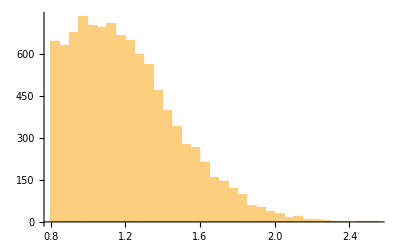

```mathematica
RandomVariate[TruncatedDistribution[{0.8,3},NormalDistribution[1,0.399]],10000];
Histogram[%]
```

```mathematica
p1=Plot[PDF[NormalDistribution[1,0.399],1.1*x-0.1],{x,0.8,3}];
Show[{mcIntfuncPlt,p1}]

NSolve[D[func[x],x]==0,x,Reals] (*Will output maximum*)
Distrib[x_,average_,var_]:=PDF[NormalDistribution[average,var],1.1*x-0.1];
n=10;
RV=RandomVariate[TruncatedDistribution[{0.8,3},NormalDistribution[1,0.399]],n];
Int=1/n Total[func[RV]/Distrib[RV,1,0.399]]*Integrate[Distrib[x,1,0.399],{x,0.8,3}]

Print[Int=1/n Total[func[RV]/Distrib[RV,1,0.399]*Integrate[Distrib[x,1,0.399],{x,0.8,3}] NIntegrate[func[x],{x,0.8,3}]]];
Print[Int2=((3-0.8)/10) Total[func[RV]]]
```

{{x→0.142636},{x→1.}}

0.664228

0.449576

1.60589